## Usage

## Initialize

```mathematica
$HistoryLength=1;
ClearAll["Global`*"];
Off[General::spell, General::spell1]
```

```mathematica
Needs["ErrorBarPlots`"]
```

## Generate global Har translation decay plots

### Reading In Parameters:

```mathematica
AALength=1717;
(* using 1717 AA because that's half of the smFLAG tag and the entire ORF of KDM5B*)
myStartTime=5;
myEndTime=65;
```

```mathematica
sampleSize = Length@onlyYellowSpots  ;
(* sampleSize usually uses the same # as sample size, in my case, number of cells*) 
repetitions = 30  ;(* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

### Reading In Files

```mathematica
analysisFolder = "/Volumes/MINI/_har TEMP use for global analysis/"
```

/Volumes/MINI/_har TEMP use for global analysis/

```mathematica
myFolders = {"/Volumes/MINI/_har TEMP use for global analysis/20180910_Har/Analysis",     "/Volumes/MINI/_har TEMP use for global analysis/20180926_harringtonine_TL_TA/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181024_har_TA/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181026_TLhar/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181027_TL_same cells as overnight_HAR/Analysis" };
```

```mathematica
myYellowOnlyFiles = Table[FileNames[(myFolders[[i]]<>"/*_ySpotNTime.m")],{i,1,Length@myFolders,1}];
Length@myYellowOnlyFiles
```

5

```mathematica
myWhiteFiles = Table[FileNames[(myFolders[[i]]<>"/*_wSpotNTime.m")],{i,1,Length@myFolders,1}];
Length@myWhiteFiles
```

5

```mathematica
myAllYellowFiles = Table[FileNames[(myFolders[[i]]<>"/*_gSpotNTime.m")],{i,1,Length@myFolders,1}];
Length@myAllYellowFiles
```

5

```mathematica
myPurpleFiles = Table[FileNames[(myFolders[[i]]<>"/*_brSpotNTime.m")],{i,1,Length@myFolders,1}];
Length@myPurpleFiles
```

5

### Yellow Only Har translation decay

```mathematica
onlyYellow = Table[Table[Import[myYellowOnlyFiles⟦i,j⟧],{j,1,Length@myYellowOnlyFiles⟦i⟧,1}],{i,1,Length@myYellowOnlyFiles,1}]//#[[2;;3]]&//Flatten[#,1]& ;
```

```mathematica
cellCount = Length@onlyYellow
```

6

```mathematica
spotCount = Total[Transpose[onlyYellow],{2}]//#[[All,2]]&;
times = Total[Transpose[onlyYellow],{2}]//#[[All,1]]/cellCount&;
```

```mathematica
yelOnlySpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*)
```

{{-178,65},{-118,61},{-58,57},{2,62},{62,55},{122,51},{182,49},{242,59},{302,59},{362,48},{422,41},{482,43},{542,40},{602,35},{662,28},{722,34},{782,33},{842,34},{902,34},{962,26},{1022,28},{1082,26},{1142,33},{1202,19},{1262,29},{1322,27},{1382,27},{1442,29},{1502,28},{1562,25},{1622,20},{1682,21},{1742,26},{1802,25},{1862,17},{1922,18},{1982,27},{2042,21},{2102,19},{2162,14},{2222,25},{2282,19},{2342,16},{2402,17},{2462,13},{2522,20},{2582,14},{2642,12},{2702,15},{2762,13},{2822,13},{2882,18},{2942,13},{3002,15},{3062,17},{3122,10},{3182,11},{3242,13},{3302,13},{3362,13},{3422,10},{3482,6},{3542,10},{3602,17},{3662,8}}

{{-178,65},{-118,61},{-58,57},{2,62},{62,55},{122,51},{182,49},{242,59},{302,59},{362,48},{422,41},{482,43},{542,40},{602,35},{662,28},{722,34},{782,33},{842,34},{902,34},{962,26},{1022,28},{1082,26},{1142,33},{1202,19},{1262,29},{1322,27},{1382,27},{1442,29},{1502,28},{1562,25},{1622,20},{1682,21},{1742,26},{1802,25},{1862,17},{1922,18},{1982,27},{2042,21},{2102,19},{2162,14},{2222,25},{2282,19},{2342,16},{2402,17},{2462,13},{2522,20},{2582,14},{2642,12},{2702,15},{2762,13},{2822,13},{2882,18},{2942,13},{3002,15},{3062,17},{3122,10},{3182,11},{3242,13},{3302,13},{3362,13},{3422,10},{3482,6},{3542,10},{3602,17},{3662,8}}

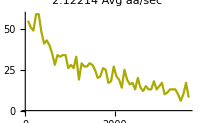
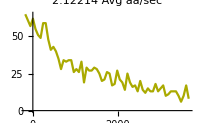
{{2.12214,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = yelOnlySpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{yelOnlyTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
myYelOnlySpotTime = spotTime;
Export[analysisFolder<>"_yOnlyGlobalTimePlot.tif",yelOnlyTimePlot];
spotTime>>analysisFolder<>"_OnlyGlobalTime.m"
```

### Yellow All Har translation decay

```mathematica
allYellow = Table[Table[Import[myAllYellowFiles[[i,j]]],{j,1,Length@myAllYellowFiles[[i]],1}],{i,1,Length@myAllYellowFiles,1}]//#[[2;;3]]&//Flatten[#,1]&;
```

```mathematica
cellCount = Length@allYellow
```

6

```mathematica
spotCount = Total[Transpose[allYellow],{2}]//#[[All,2]]&;
```

```mathematica
yelAllSpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*)
```

{{-178,109},{-118,103},{-58,91},{2,91},{62,92},{122,79},{182,86},{242,87},{302,88},{362,79},{422,69},{482,63},{542,70},{602,67},{662,54},{722,64},{782,65},{842,59},{902,61},{962,51},{1022,49},{1082,51},{1142,53},{1202,44},{1262,55},{1322,53},{1382,55},{1442,48},{1502,50},{1562,50},{1622,40},{1682,42},{1742,47},{1802,42},{1862,33},{1922,40},{1982,42},{2042,37},{2102,33},{2162,29},{2222,39},{2282,34},{2342,29},{2402,27},{2462,30},{2522,32},{2582,30},{2642,29},{2702,27},{2762,26},{2822,20},{2882,29},{2942,22},{3002,26},{3062,25},{3122,13},{3182,18},{3242,19},{3302,21},{3362,16},{3422,13},{3482,13},{3542,14},{3602,21},{3662,15}}

{{-178,109},{-118,103},{-58,91},{2,91},{62,92},{122,79},{182,86},{242,87},{302,88},{362,79},{422,69},{482,63},{542,70},{602,67},{662,54},{722,64},{782,65},{842,59},{902,61},{962,51},{1022,49},{1082,51},{1142,53},{1202,44},{1262,55},{1322,53},{1382,55},{1442,48},{1502,50},{1562,50},{1622,40},{1682,42},{1742,47},{1802,42},{1862,33},{1922,40},{1982,42},{2042,37},{2102,33},{2162,29},{2222,39},{2282,34},{2342,29},{2402,27},{2462,30},{2522,32},{2582,30},{2642,29},{2702,27},{2762,26},{2822,20},{2882,29},{2942,22},{3002,26},{3062,25},{3122,13},{3182,18},{3242,19},{3302,21},{3362,16},{3422,13},{3482,13},{3542,14},{3602,21},{3662,15}}

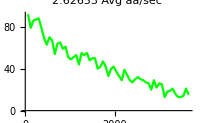
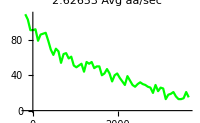
{{2.62653,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = yelAllSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{yelAllTimePlot=spotTime//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
yelAllTime = spotTime;
Export[analysisFolder<>"_yAllGlobalTimePlot.tif",yelAllTimePlot];
yelAllTimePlot>>analysisFolder<>"_yAllGlobalTime.m"
```

### White Har translation decay

```mathematica
white = Table[Table[Import[myWhiteFiles[[i,j]]],{j,1,Length@myWhiteFiles[[i]],1}],{i,1,Length@myWhiteFiles,1}]//#[[2;;3]]&//Flatten[#,1]&;
```

```mathematica
cellCount = Length@white
```

6

```mathematica
spotCount = Total[Transpose[white],{2}]//#[[All,2]]&;
times = Total[Transpose[white],{2}]//#[[All,1]]/cellCount&;
```

```mathematica
whiteSpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*)
```

{{-178,44},{-118,42},{-58,34},{2,29},{62,37},{122,28},{182,37},{242,28},{302,29},{362,31},{422,28},{482,20},{542,30},{602,32},{662,26},{722,30},{782,32},{842,25},{902,27},{962,25},{1022,21},{1082,25},{1142,20},{1202,25},{1262,26},{1322,26},{1382,28},{1442,19},{1502,22},{1562,25},{1622,20},{1682,21},{1742,21},{1802,17},{1862,16},{1922,22},{1982,15},{2042,16},{2102,14},{2162,15},{2222,14},{2282,15},{2342,13},{2402,10},{2462,17},{2522,12},{2582,16},{2642,17},{2702,12},{2762,13},{2822,7},{2882,11},{2942,9},{3002,11},{3062,8},{3122,3},{3182,7},{3242,6},{3302,8},{3362,3},{3422,3},{3482,7},{3542,4},{3602,4},{3662,7}}

{{-178,44},{-118,42},{-58,34},{2,29},{62,37},{122,28},{182,37},{242,28},{302,29},{362,31},{422,28},{482,20},{542,30},{602,32},{662,26},{722,30},{782,32},{842,25},{902,27},{962,25},{1022,21},{1082,25},{1142,20},{1202,25},{1262,26},{1322,26},{1382,28},{1442,19},{1502,22},{1562,25},{1622,20},{1682,21},{1742,21},{1802,17},{1862,16},{1922,22},{1982,15},{2042,16},{2102,14},{2162,15},{2222,14},{2282,15},{2342,13},{2402,10},{2462,17},{2522,12},{2582,16},{2642,17},{2702,12},{2762,13},{2822,7},{2882,11},{2942,9},{3002,11},{3062,8},{3122,3},{3182,7},{3242,6},{3302,8},{3362,3},{3422,3},{3482,7},{3542,4},{3602,4},{3662,7}}

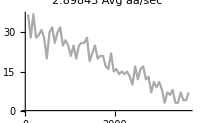
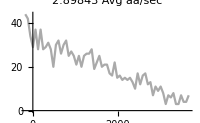
{{2.89843,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = whiteSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{whiteTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
whiteTime = spotTime
```

{{-178,44},{-118,42},{-58,34},{2,29},{62,37},{122,28},{182,37},{242,28},{302,29},{362,31},{422,28},{482,20},{542,30},{602,32},{662,26},{722,30},{782,32},{842,25},{902,27},{962,25},{1022,21},{1082,25},{1142,20},{1202,25},{1262,26},{1322,26},{1382,28},{1442,19},{1502,22},{1562,25},{1622,20},{1682,21},{1742,21},{1802,17},{1862,16},{1922,22},{1982,15},{2042,16},{2102,14},{2162,15},{2222,14},{2282,15},{2342,13},{2402,10},{2462,17},{2522,12},{2582,16},{2642,17},{2702,12},{2762,13},{2822,7},{2882,11},{2942,9},{3002,11},{3062,8},{3122,3},{3182,7},{3242,6},{3302,8},{3362,3},{3422,3},{3482,7},{3542,4},{3602,4},{3662,7}}

```mathematica
Export[analysisFolder<>"_wGlobalTimePlot.tif",whiteTimePlot];
whiteTimePlot>>analysisFolder<>"_wGlobalTime.m"
```

### Purple Har translation decay

```mathematica
purple = Table[Table[Import[myPurpleFiles[[i,j]]],{j,1,Length@myPurpleFiles[[i]],1}],{i,1,Length@myPurpleFiles,1}]//#[[2;;3]]&//Flatten[#,1]&;
```

```mathematica
cellCount = Length@purple
```

6

```mathematica
spotCount = Total[Transpose[purple],{2}]//#[[All,2]]&;
times = Total[Transpose[purple],{2}]//#[[All,1]]/cellCount&;
purpleSpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*)
```

{{-178,151},{-118,152},{-58,128},{2,130},{62,142},{122,142},{182,144},{242,150},{302,141},{362,145},{422,134},{482,154},{542,146},{602,145},{662,157},{722,138},{782,155},{842,151},{902,157},{962,149},{1022,136},{1082,146},{1142,138},{1202,149},{1262,149},{1322,151},{1382,153},{1442,145},{1502,168},{1562,154},{1622,155},{1682,139},{1742,144},{1802,134},{1862,137},{1922,131},{1982,141},{2042,148},{2102,150},{2162,149},{2222,134},{2282,160},{2342,150},{2402,154},{2462,144},{2522,158},{2582,149},{2642,157},{2702,148},{2762,142},{2822,149},{2882,145},{2942,143},{3002,164},{3062,146},{3122,148},{3182,151},{3242,132},{3302,136},{3362,138},{3422,157},{3482,153},{3542,144},{3602,141},{3662,152}}

{{-178,151},{-118,152},{-58,128},{2,130},{62,142},{122,142},{182,144},{242,150},{302,141},{362,145},{422,134},{482,154},{542,146},{602,145},{662,157},{722,138},{782,155},{842,151},{902,157},{962,149},{1022,136},{1082,146},{1142,138},{1202,149},{1262,149},{1322,151},{1382,153},{1442,145},{1502,168},{1562,154},{1622,155},{1682,139},{1742,144},{1802,134},{1862,137},{1922,131},{1982,141},{2042,148},{2102,150},{2162,149},{2222,134},{2282,160},{2342,150},{2402,154},{2462,144},{2522,158},{2582,149},{2642,157},{2702,148},{2762,142},{2822,149},{2882,145},{2942,143},{3002,164},{3062,146},{3122,148},{3182,151},{3242,132},{3302,136},{3362,138},{3422,157},{3482,153},{3542,144},{3602,141},{3662,152}}

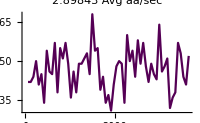
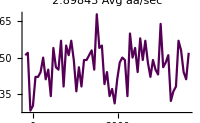
{{2.89843,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = purpleSpotCount
purpleSpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{purpleTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
purpleTime = spotTime
```

{{-178,151},{-118,152},{-58,128},{2,130},{62,142},{122,142},{182,144},{242,150},{302,141},{362,145},{422,134},{482,154},{542,146},{602,145},{662,157},{722,138},{782,155},{842,151},{902,157},{962,149},{1022,136},{1082,146},{1142,138},{1202,149},{1262,149},{1322,151},{1382,153},{1442,145},{1502,168},{1562,154},{1622,155},{1682,139},{1742,144},{1802,134},{1862,137},{1922,131},{1982,141},{2042,148},{2102,150},{2162,149},{2222,134},{2282,160},{2342,150},{2402,154},{2462,144},{2522,158},{2582,149},{2642,157},{2702,148},{2762,142},{2822,149},{2882,145},{2942,143},{3002,164},{3062,146},{3122,148},{3182,151},{3242,132},{3302,136},{3362,138},{3422,157},{3482,153},{3542,144},{3602,141},{3662,152}}

```mathematica
Export[analysisFolder<>"_pGlobalTimePlot.tif",purpleTimePlot];
purpleSpotWeights>>analysisFolder<>"_pGlobalTime.m"
```

### View it all...

```mathematica
Row[{purpleTimePlot,whiteTimePlot,yelOnlyTimePlot,yelAllTimePlot
}]
```

-Graphics--Graphics--Graphics--Graphics-

## Bootstrapping the datasets:

### Reading In BS Parameters:

```mathematica
sampleSize = Length@onlyYellowSpots  
(* sampleSize usually uses the same # as sample size, in my case, number of cells*) 
repetitions = 30  (* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

6

30

### BS for Only Yellow Spots:

```mathematica
onlyYellow//Dimensions
```

{6,65,2}

```mathematica
onlyYellowSpots = onlyYellow[[All,All,2]];
onlyYellowSpots;
```

```mathematica
(*
DEV: 
I dont think this is right..need one error of all the means instead of the dev of data from each mean 

stdevsBS = Table[Table[StandardDeviation[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]//Transpose;
errorBS = Table[ErrorBar/@stdevsBS[[i]],{i,1,Length@stdevsBS,1}];
b = Table[Transpose[{meanTimeBS[[i]],errorBS[[i]]}],{i,1,Length@meansBS,1}];
Dimensions/@b
Dimensions/@meansBS
meanTimeBS = Table[Transpose[{Table[times,Length@meansBS][[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];

*)
```

```mathematica
a = Table[Table[Table[RandomChoice[onlyYellowSpots[[All,i]]],sampleSize],repetitions ],{i,1,Length@yelOnlySpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

{{5.5,9.5,9.33333,9.33333,12.6667,6.,6.33333,10.5,14.,8.33333,8.,12.6667,13.3333,15.,10.8333,6.5,6.66667,13.3333,12.5,7.,14.,13.1667,7.66667,13.,5.5,15.5,10.8333,10.8333,8.66667,7.5},{9.66667,9.16667,12.6667,12.6667,7.33333,7.83333,7.16667,10.6667,9.,11.3333,8.16667,11.5,4.5,10.3333,13.5,6.33333,8.,15.5,11.3333,13.1667,8.33333,7.83333,11.5,10.3333,10.6667,19.3333,10.1667,10.1667,7.,6.},{8.5,11.1667,4.5,9.83333,9.,8.66667,11.,6.33333,7.83333,5.5,9.33333,7.5,7.83333,8.66667,13.1667,10.3333,13.5,8.33333,11.1667,9.5,11.1667,6.33333,11.5,8.66667,7.5,10.3333,7.,8.83333,3.66667,10.3333},{13.5,8.83333,16.6667,9.33333,9.5,14.3333,12.6667,11.1667,12.6667,11.1667,11.,7.83333,10.3333,7.16667,5.,10.3333,11.8333,9.,8.83333,9.5,6.33333,9.5,8.66667,13.5,7.16667,6.33333,8.83333,11.1667,13.3333,10.3333},{9.5,10.1667,8.83333,8.33333,10.1667,10.8333,6.66667,9.16667,8.66667,8.66667,9.83333,8.5,9.33333,10.5,8.33333,6.66667,10.8333,10.,10.5,11.3333,7.,10.1667,9.,8.33333,7.83333,7.33333,10.3333,13.1667,10.1667,11.},{7.,10.5,8.5,8.5,5.5,11.,10.,11.,6.5,6.5,10.5,13.,10.5,10.5,8.5,11.,9.,6.5,7.5,7.,6.5,9.,13.,9.,8.5,5.5,8.5,8.5,10.5,6.},{10.3333,10.5,5.33333,8.83333,8.5,8.83333,7.83333,6.66667,9.,8.16667,7.83333,8.5,8.,11.3333,10.8333,10.5,5.16667,4.5,3.66667,8.16667,5.83333,4.66667,14.6667,7.83333,12.6667,8.83333,7.,9.,6.33333,8.5},{8.83333,12.5,7.,10.8333,9.66667,10.1667,7.5,10.5,9.16667,9.33333,10.3333,10.3333,9.33333,8.33333,9.83333,9.16667,11.1667,12.5,12.3333,10.,11.5,12.,7.83333,9.,10.,9.33333,10.5,6.83333,9.33333,9.},{11.8333,11.,9.66667,7.16667,12.,13.5,8.66667,6.83333,9.83333,7.83333,7.33333,12.1667,12.3333,14.5,9.33333,8.83333,6.5,11.3333,10.8333,10.3333,6.66667,16.5,12.,7.83333,8.83333,8.,7.5,7.16667,11.1667,8.83333},{8.,8.,7.16667,8.66667,7.5,7.,8.5,7.16667,8.66667,6.66667,8.83333,8.83333,6.16667,9.83333,8.83333,10.5,10.,5.83333,6.16667,10.1667,8.83333,5.66667,6.,6.16667,3.66667,10.3333,9.,9.,6.66667,7.33333},{6.5,5.,7.66667,5.33333,7.5,5.83333,4.33333,9.,6.83333,5.16667,7.5,6.5,8.16667,6.83333,8.5,5.83333,8.83333,7.33333,8.5,6.83333,4.66667,7.83333,6.83333,6.16667,9.83333,8.,6.33333,8.,3.83333,6.5},{5.,6.5,4.83333,8.16667,7.,8.5,6.33333,6.5,6.5,6.66667,4.33333,5.,6.66667,9.33333,7.66667,6.66667,7.83333,7.83333,5.,5.33333,8.,7.33333,8.,7.,5.66667,5.66667,6.,9.16667,8.,5.83333},{5.66667,5.33333,9.,6.,9.33333,8.66667,8.,5.83333,9.,5.16667,4.33333,8.,6.,8.16667,7.16667,5.5,10.,9.5,7.33333,5.5,5.83333,9.,8.66667,5.,5.83333,8.5,6.,5.5,5.33333,6.83333},{6.,6.66667,4.5,4.66667,7.16667,5.33333,3.83333,5.,5.16667,3.33333,6.33333,7.16667,5.,4.,4.66667,6.33333,6.33333,4.5,6.66667,5.16667,4.66667,5.16667,7.,8.16667,4.,4.,7.,5.83333,7.,4.66667},{5.16667,6.,5.16667,5.16667,4.5,4.5,4.66667,4.83333,5.5,5.66667,4.5,4.5,4.5,3.5,5.33333,4.5,4.83333,4.66667,5.5,5.5,4.66667,5.5,5.5,5.16667,5.5,5.16667,4.16667,5.66667,4.,5.16667},{4.,7.66667,5.,5.,6.5,7.83333,4.5,7.83333,5.66667,4.83333,4.33333,4.66667,4.33333,7.,4.83333,6.33333,7.,6.33333,5.66667,5.66667,9.16667,6.33333,4.16667,6.83333,6.,3.83333,6.5,3.66667,8.33333,5.66667},{5.33333,3.83333,6.16667,7.,5.,6.66667,4.5,5.83333,6.16667,6.,7.16667,4.83333,6.16667,4.66667,4.33333,3.66667,6.33333,5.33333,3.16667,5.,4.83333,5.33333,7.16667,5.66667,4.66667,4.33333,8.,4.5,6.33333,4.66667},{6.5,5.16667,5.,6.,6.,5.5,6.5,5.33333,5.33333,4.66667,5.33333,6.,4.83333,6.33333,4.83333,5.83333,6.33333,7.83333,4.66667,5.33333,7.33333,5.66667,4.5,6.16667,6.16667,6.66667,7.,5.33333,5.66667,5.},{4.83333,7.16667,4.,6.,7.,6.33333,4.66667,5.83333,6.66667,6.83333,6.5,5.5,6.16667,6.16667,5.,6.33333,7.16667,6.83333,5.33333,6.16667,4.,3.,4.33333,6.5,5.16667,5.5,5.16667,6.16667,4.66667,5.33333},{4.,4.66667,6.33333,4.66667,2.,4.33333,2.66667,4.,5.33333,4.66667,3.33333,4.33333,5.,4.,4.33333,4.66667,5.33333,4.,4.66667,3.66667,5.33333,4.66667,5.33333,4.33333,4.33333,4.,5.33333,4.33333,5.,4.},{4.66667,3.83333,6.,4.33333,4.5,5.,5.16667,4.33333,4.16667,6.33333,2.66667,4.,4.16667,4.5,4.16667,3.16667,3.5,6.66667,5.83333,6.,4.,4.5,4.,4.,5.16667,5.66667,5.33333,3.16667,5.83333,6.5},{5.5,2.66667,5.16667,4.16667,6.83333,3.5,4.33333,3.16667,1.66667,6.83333,5.33333,4.33333,5.16667,5.,2.5,4.16667,2.83333,2.33333,4.,3.83333,7.,4.83333,5.,5.83333,2.5,4.16667,5.16667,4.5,4.33333,3.66667},{7.,6.5,7.,5.,4.5,6.16667,5.16667,6.5,4.66667,7.66667,3.,7.,5.,6.33333,4.16667,6.,5.5,5.16667,4.5,4.,7.66667,4.83333,8.83333,3.66667,4.66667,4.83333,7.83333,3.83333,5.66667,4.33333},{2.16667,3.,3.83333,3.5,2.83333,3.5,3.5,2.83333,2.16667,2.66667,3.33333,3.66667,3.,2.83333,3.66667,2.66667,4.,2.5,2.66667,3.83333,4.33333,3.83333,2.33333,3.5,3.83333,2.83333,3.66667,2.83333,2.66667,3.5},{3.83333,4.66667,5.33333,5.,4.,5.16667,4.83333,5.83333,4.5,5.33333,7.,5.83333,5.66667,4.83333,4.,3.83333,2.16667,4.,3.5,6.16667,6.,7.83333,5.5,6.,6.,5.66667,3.83333,6.,3.,4.},{3.5,4.,4.5,3.66667,3.66667,4.,3.66667,4.,5.33333,4.66667,3.83333,5.66667,5.16667,3.5,5.33333,4.66667,3.66667,5.5,5.33333,4.16667,4.5,6.5,4.83333,4.5,4.16667,5.33333,4.83333,5.16667,5.33333,5.16667},{5.,3.16667,4.5,5.5,4.33333,4.16667,5.,3.83333,4.5,3.16667,5.83333,4.,3.66667,4.33333,5.5,5.66667,5.5,4.,3.5,4.33333,3.,4.,5.33333,4.,3.66667,4.,5.33333,4.66667,5.,5.66667},{3.16667,4.83333,7.66667,4.66667,6.33333,6.,5.33333,5.66667,4.,6.66667,5.,4.33333,4.16667,5.5,4.66667,5.16667,5.,6.16667,4.83333,4.66667,3.66667,5.16667,4.16667,4.66667,5.66667,5.16667,4.33333,4.33333,3.66667,3.5},{3.83333,5.33333,4.,5.83333,4.33333,3.,4.5,4.,4.,4.66667,3.66667,5.,5.83333,4.66667,6.33333,5.66667,5.33333,4.33333,4.83333,5.83333,4.83333,5.66667,3.66667,5.,5.5,4.66667,4.66667,5.33333,4.83333,3.5},{5.,3.5,3.,5.33333,2.16667,4.,4.,4.,4.,4.,5.5,2.66667,5.5,3.5,3.5,4.16667,3.16667,5.,2.83333,4.,4.5,2.83333,4.5,4.16667,3.,3.16667,3.33333,5.33333,4.83333,4.5},{4.5,4.16667,3.83333,3.33333,3.5,2.66667,2.16667,2.16667,3.66667,3.16667,3.83333,4.,4.5,2.83333,4.,3.16667,2.5,3.83333,4.,4.16667,2.5,3.33333,3.33333,1.5,3.16667,3.16667,2.33333,2.5,3.16667,3.16667},{4.,3.33333,2.16667,3.33333,4.16667,3.83333,5.,3.16667,3.83333,3.83333,3.33333,3.33333,3.5,3.5,4.,2.33333,3.33333,3.5,4.,4.5,3.83333,2.33333,4.33333,3.,4.66667,5.,2.66667,2.83333,4.33333,4.},{5.33333,3.33333,3.5,4.16667,3.,4.33333,4.33333,4.33333,4.16667,5.,6.,5.,4.,3.16667,4.83333,5.5,4.5,3.83333,5.5,4.83333,3.5,3.,4.33333,4.5,4.33333,5.83333,3.16667,5.83333,3.66667,4.33333},{3.,4.66667,2.5,4.66667,2.5,5.66667,2.,5.66667,2.66667,3.16667,6.5,4.,3.16667,5.16667,2.16667,4.66667,3.33333,4.66667,5.66667,5.16667,4.83333,2.5,5.33333,5.16667,3.16667,4.16667,5.33333,4.16667,7.83333,5.},{2.33333,2.33333,4.33333,3.,3.66667,3.,1.66667,3.66667,2.33333,3.16667,2.5,2.5,3.16667,5.,1.5,1.33333,2.5,4.33333,1.33333,3.33333,3.16667,1.66667,3.5,3.66667,2.16667,3.66667,4.33333,2.5,2.33333,3.5},{3.33333,2.33333,3.5,2.66667,2.83333,3.16667,2.66667,3.83333,2.83333,4.16667,3.33333,2.33333,3.,3.33333,3.,3.16667,3.33333,3.5,4.16667,3.16667,3.5,2.16667,3.33333,2.5,3.16667,2.5,2.16667,2.83333,3.66667,3.83333},{4.33333,5.33333,5.,4.,3.83333,4.5,3.83333,2.5,4.,3.66667,3.83333,4.,3.33333,4.66667,3.66667,4.33333,4.83333,3.16667,5.,3.16667,5.,3.83333,4.16667,3.83333,4.5,5.,5.5,4.,2.5,3.83333},{2.83333,1.5,2.66667,5.,3.33333,5.,4.83333,2.83333,2.83333,3.5,4.,4.33333,2.16667,4.83333,2.5,4.16667,3.5,4.33333,4.,5.33333,5.,5.5,1.83333,3.16667,4.33333,3.,1.33333,2.33333,3.,4.66667},{2.,2.5,4.33333,2.,3.66667,3.16667,3.,3.5,3.5,4.33333,2.16667,2.66667,2.5,3.,3.16667,4.16667,1.,3.16667,3.66667,2.5,3.5,3.,3.83333,2.83333,3.66667,2.,3.16667,2.5,3.66667,4.},{3.16667,1.5,2.,1.5,1.83333,2.5,2.33333,2.16667,3.5,3.,2.16667,2.66667,1.83333,2.83333,2.16667,2.16667,1.66667,2.33333,2.66667,2.33333,1.66667,1.83333,2.16667,3.,2.,2.16667,3.,2.33333,3.66667,2.83333},{3.5,5.33333,4.66667,2.83333,3.83333,4.83333,4.,2.83333,4.5,4.5,5.16667,4.66667,4.33333,4.16667,3.83333,4.,5.,4.5,3.16667,4.83333,4.,4.16667,3.83333,4.66667,5.,3.83333,4.16667,3.,3.,3.83333},{4.16667,3.33333,3.,3.33333,4.,2.83333,3.16667,2.33333,3.33333,2.66667,4.33333,3.66667,3.,4.33333,3.5,4.16667,3.16667,3.16667,3.,4.16667,3.,3.33333,3.33333,3.16667,3.16667,3.66667,3.33333,2.83333,4.,3.16667},{2.,2.66667,1.66667,2.5,2.5,3.16667,2.66667,3.,2.33333,2.33333,2.5,1.33333,3.,2.5,2.33333,3.33333,3.33333,3.16667,2.16667,1.33333,2.83333,2.5,2.5,3.66667,4.,2.66667,2.66667,3.83333,2.,1.83333},{3.16667,3.,2.5,3.16667,2.,2.66667,2.66667,3.,3.16667,3.66667,2.83333,3.16667,3.5,3.33333,2.33333,3.16667,3.16667,3.33333,2.66667,2.66667,2.16667,2.5,2.16667,2.83333,3.5,2.66667,2.5,3.,2.83333,3.33333},{2.16667,1.5,2.33333,1.83333,2.,2.66667,2.83333,2.66667,2.66667,2.16667,2.33333,2.,2.,3.16667,3.16667,1.83333,1.66667,2.33333,2.,2.33333,2.,3.33333,2.16667,2.66667,1.66667,1.5,2.16667,2.,1.83333,2.5},{3.66667,2.,3.66667,1.,2.33333,1.66667,1.66667,1.66667,4.33333,3.,1.33333,3.66667,3.,2.,3.33333,2.,3.33333,3.,3.66667,3.,3.66667,3.66667,3.66667,3.33333,2.,1.66667,4.33333,3.33333,3.66667,3.33333},{2.33333,3.,3.16667,2.5,1.83333,2.66667,2.83333,2.33333,2.33333,2.83333,2.,1.66667,2.66667,2.66667,2.5,1.5,2.83333,1.5,2.5,2.,1.83333,2.66667,2.16667,1.83333,3.5,2.16667,1.66667,2.16667,1.66667,2.5},{2.,2.5,3.33333,1.83333,2.16667,1.,3.,1.33333,2.16667,2.16667,1.83333,1.16667,0.833333,2.83333,2.16667,1.,2.,2.83333,1.5,1.16667,3.16667,1.83333,1.5,2.,1.66667,3.16667,2.66667,1.33333,2.,1.33333},{2.83333,2.66667,3.,2.66667,2.66667,1.66667,1.33333,2.16667,2.5,1.83333,4.16667,1.66667,2.66667,3.33333,3.16667,2.33333,2.33333,2.16667,3.,2.83333,2.66667,2.83333,2.5,3.66667,0.666667,2.33333,1.66667,2.5,1.,2.16667},{1.5,2.33333,2.16667,1.33333,1.16667,2.83333,2.5,1.83333,1.33333,1.83333,1.,1.83333,2.16667,1.33333,2.33333,1.83333,2.5,2.5,1.66667,2.,2.66667,1.83333,3.33333,4.,1.5,2.66667,2.16667,1.33333,3.83333,2.16667},{1.5,2.83333,2.5,1.83333,1.33333,2.33333,2.,2.33333,2.16667,2.66667,2.33333,1.66667,2.66667,1.66667,2.16667,2.66667,2.66667,1.5,1.66667,2.16667,2.16667,2.,1.83333,2.5,1.66667,1.66667,1.83333,2.83333,1.5,1.66667},{2.5,4.33333,2.83333,2.66667,4.83333,3.5,3.,2.,1.83333,3.5,3.,3.83333,3.,2.16667,1.66667,3.,2.5,3.5,4.16667,3.5,3.5,2.66667,2.83333,3.66667,1.83333,2.83333,1.66667,2.66667,2.16667,4.16667},{2.5,2.16667,2.5,1.66667,1.83333,2.,2.,1.83333,2.66667,2.5,2.16667,2.,2.33333,2.33333,2.66667,1.83333,2.66667,1.66667,2.5,1.83333,2.83333,2.,1.5,2.5,2.5,2.33333,2.83333,2.83333,2.,2.33333},{3.16667,3.66667,2.33333,1.83333,3.,2.33333,2.,3.5,1.66667,1.83333,2.5,4.16667,2.33333,2.16667,0.666667,1.83333,2.,1.83333,3.33333,1.66667,2.5,1.16667,3.16667,3.16667,3.16667,2.5,4.33333,2.5,4.33333,2.5},{1.5,1.83333,1.83333,2.,3.33333,2.66667,2.16667,2.16667,3.33333,4.66667,2.5,2.5,2.5,1.5,2.,2.83333,2.83333,4.16667,2.16667,3.16667,4.16667,2.33333,3.16667,3.5,3.83333,1.5,3.16667,2.66667,1.5,1.83333},{1.5,2.66667,2.,1.5,1.83333,1.5,0.666667,2.,2.33333,1.83333,1.5,2.66667,1.5,1.66667,2.16667,1.66667,2.5,3.,1.83333,2.16667,1.33333,1.83333,1.33333,1.83333,1.66667,1.16667,3.,1.5,2.5,2.16667},{1.66667,1.33333,2.33333,1.83333,1.16667,1.16667,2.16667,1.5,2.33333,1.83333,1.5,1.16667,1.83333,1.83333,2.5,1.33333,1.66667,2.16667,2.33333,2.5,1.33333,1.83333,2.33333,2.,2.16667,1.83333,2.33333,1.33333,2.,1.66667},{2.,2.,2.,2.5,2.5,2.16667,2.16667,2.66667,2.16667,2.33333,1.5,2.,2.,2.,2.66667,1.83333,1.83333,1.66667,1.83333,2.5,1.66667,2.83333,2.33333,2.,1.83333,2.33333,2.33333,2.5,2.,2.33333},{3.5,2.5,2.66667,2.16667,2.83333,1.66667,2.,2.16667,2.,1.66667,1.83333,2.16667,2.66667,2.66667,1.83333,1.83333,3.5,2.33333,2.83333,2.16667,4.,2.,3.33333,1.33333,1.16667,1.5,1.5,2.66667,1.5,2.83333},{2.,2.16667,2.33333,2.5,0.666667,1.,1.66667,1.83333,1.,1.66667,1.83333,1.,3.5,3.33333,1.66667,2.33333,3.16667,3.16667,2.5,2.,2.5,2.5,2.83333,1.83333,2.5,1.16667,3.16667,1.83333,2.83333,1.66667},{1.66667,1.66667,1.5,2.16667,2.,1.5,1.83333,1.83333,1.83333,1.33333,1.5,1.5,1.33333,1.83333,1.33333,1.83333,1.33333,1.83333,1.66667,1.33333,1.5,2.33333,1.66667,1.83333,1.16667,1.5,2.,1.5,1.33333,1.66667},{0.666667,1.66667,0.666667,1.33333,1.66667,1.33333,1.33333,1.33333,1.,0.666667,0.333333,1.,1.,1.66667,0.666667,0.666667,0.666667,0.666667,1.33333,1.33333,1.33333,0.666667,0.666667,1.,1.66667,1.,1.,1.33333,1.33333,1.33333},{1.,0.833333,1.66667,2.,1.5,1.33333,1.83333,1.66667,2.,1.16667,1.5,2.16667,2.16667,2.16667,2.,2.,1.,1.33333,2.,2.16667,1.83333,1.83333,1.66667,2.16667,2.16667,1.66667,1.83333,1.33333,1.83333,1.16667},{2.83333,3.33333,2.83333,3.,2.,3.,2.16667,1.,3.5,3.83333,3.16667,2.33333,2.83333,2.16667,2.33333,3.5,2.83333,3.16667,3.33333,2.33333,3.,3.5,2.,3.66667,2.83333,2.66667,3.,3.33333,2.83333,2.5},{1.,1.,0.833333,1.5,0.666667,1.66667,2.16667,1.16667,1.66667,1.5,0.833333,0.5,1.5,1.33333,1.16667,1.16667,1.33333,1.33333,1.66667,1.,1.,1.16667,1.,1.16667,1.5,1.16667,1.,1.83333,1.16667,1.16667}}

{3.07642,3.04112,2.31545,2.63526,1.486,2.07863,2.4478,1.50037,2.51468,1.64555,1.46112,1.32304,1.65745,1.23792,0.571346,1.43929,1.14782,0.821972,1.04674,0.84388,1.04742,1.35537,1.4234,0.584523,1.21669,0.772471,0.824764,0.993738,0.817356,0.909086,0.748541,0.736826,0.869539,1.40753,0.954672,0.547256,0.749819,1.17585,0.786236,0.566295,0.696736,0.514788,0.658475,0.427353,0.480959,0.937102,0.511334,0.706226,0.743555,0.733895,0.45006,0.826678,0.380898,0.898789,0.86296,0.544008,0.422091,0.328558,0.699868,0.753133,0.275894,0.378375,0.399713,0.605662,0.354725}

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{7.66667,12.6667,5.83333,10.6667,15.8333,11.,7.66667,14.6667,4.5,9.66667,7.66667,13.,11.1667,16.8333,12.6667,11.8333,8.5,14.8333,13.5,7.33333,7.,7.83333,7.16667,8.66667,10.8333,5.83333,6.5,7.,10.5,8.33333}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{myYelOnlySpotTime ,errorBS}];
```

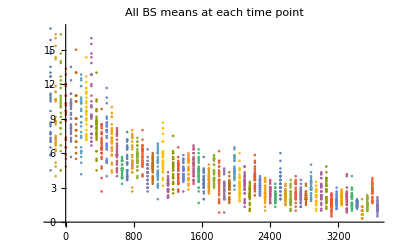

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

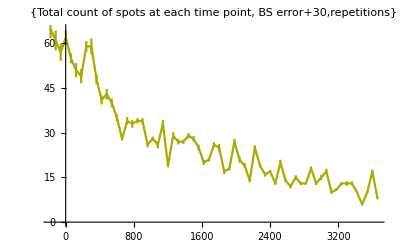

```mathematica
ErrorListPlot[b,PlotStyle->{Darker[Yellow]}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```

### BS for All Yellow Spots:

```mathematica
allYellow//Dimensions
```

{6,65,2}

```mathematica
allYellowSpots = allYellow[[All,All,2]];
allYellowSpots
```

{{8,10,11,11,9,10,9,10,14,9,7,6,9,8,8,8,6,6,6,8,7,7,4,7,3,6,7,7,7,10,8,7,7,8,7,7,8,9,7,3,8,6,6,4,6,4,4,2,5,4,4,7,6,5,3,4,3,6,6,5,3,4,3,4,4},{25,25,21,25,23,12,21,22,17,25,20,22,23,20,13,24,19,18,20,16,17,22,22,13,19,20,17,14,21,17,18,12,19,17,12,15,13,8,7,11,8,9,12,8,11,12,10,12,12,8,7,5,5,10,9,3,4,4,9,4,1,3,3,7,3},{10,10,5,3,12,9,7,8,7,7,4,6,7,6,4,7,6,8,4,5,4,1,4,7,8,4,3,2,4,2,1,5,3,1,1,1,3,0,0,1,1,2,2,3,2,2,3,4,0,2,1,5,0,2,2,0,2,2,1,1,2,0,0,4,0},{7,5,10,10,9,7,8,6,8,8,7,6,6,6,5,4,4,5,5,3,5,4,4,2,1,3,4,5,2,2,3,3,3,0,2,3,3,3,2,1,3,2,1,1,1,2,1,1,2,1,1,1,1,1,2,2,2,2,2,1,2,2,2,0,1},{33,31,24,22,18,20,26,18,25,16,13,9,11,12,6,9,12,9,9,8,8,8,9,5,13,9,12,9,8,8,4,6,8,7,7,5,8,9,8,7,8,5,3,6,4,10,6,6,2,5,3,5,5,7,4,4,4,3,2,4,3,2,3,3,5},{26,22,20,20,21,21,15,23,17,14,18,14,14,15,18,12,18,13,17,11,8,9,10,10,11,11,12,11,8,11,6,9,7,9,4,9,7,8,9,6,11,10,5,5,6,2,6,4,6,6,4,6,5,1,5,0,3,2,1,1,2,2,3,3,2}}

```mathematica
(*
DEV: 
I dont think this is right..need one error of all the means instead of the dev of data from each mean 

stdevsBS = Table[Table[StandardDeviation[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]//Transpose;
errorBS = Table[ErrorBar/@stdevsBS[[i]],{i,1,Length@stdevsBS,1}];
b = Table[Transpose[{meanTimeBS[[i]],errorBS[[i]]}],{i,1,Length@meansBS,1}];
Dimensions/@b
Dimensions/@meansBS
meanTimeBS = Table[Transpose[{Table[times,Length@meansBS][[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];

*)
```

```mathematica
a = Table[Table[Table[RandomChoice[allYellowSpots[[All,i]]],sampleSize],repetitions ],{i,1,Length@yelAllSpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

{3.94448,4.19161,2.84958,3.08871,2.39505,1.96165,2.67706,3.554,2.15684,2.22651,2.79262,2.07918,1.81632,1.92231,2.11291,2.33002,2.18072,1.74059,2.5692,1.84765,1.90557,2.35283,2.5836,1.33978,2.55004,1.97966,2.38479,1.58356,2.37229,1.88104,1.67432,1.25105,2.07186,2.14757,1.42847,1.72151,1.47661,1.09679,1.05816,1.41715,1.36804,1.11962,1.08956,0.793271,1.30746,2.04299,1.00797,1.40312,1.86916,1.15547,0.778954,0.653241,1.07344,1.32464,1.05929,0.596097,0.367458,0.488174,1.2313,0.665132,0.289283,0.40337,0.394769,1.1944,0.668604}

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{21.1667,18.,18.5,23.6667,20.8333,17.,23.6667,17.6667,22.5,20.3333,23.,16.1667,23.3333,18.5,14.,11.8333,25.,17.6667,18.1667,10.8333,20.8333,16.8333,20.,18.5,21.8333,15.1667,28.,18.6667,25.,15.8333}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{yelAllTime ,errorBS}];
```

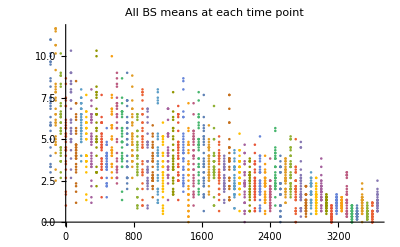

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

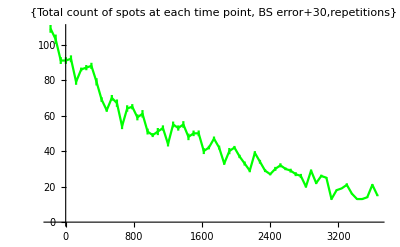

```mathematica
ErrorListPlot[b,PlotStyle->{Green}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```

### BS for White Spots:

```mathematica
white//Dimensions
```

{6,65,2}

```mathematica
white = white[[All,All,2]];
white
```

{{2,2,4,5,4,3,4,2,3,2,3,3,5,2,3,4,1,1,1,3,3,2,1,2,1,2,2,2,2,5,4,5,4,2,4,6,2,6,0,2,1,1,2,2,4,0,1,1,1,1,2,1,2,1,2,0,2,2,1,0,1,2,1,1,3},{11,10,9,10,8,5,11,10,11,13,8,8,12,10,7,12,8,8,12,9,8,13,11,10,11,12,13,11,12,10,11,7,10,7,5,10,5,6,3,7,4,5,6,5,7,8,6,9,7,7,3,2,2,5,2,2,2,1,5,2,0,3,2,3,1},{7,9,3,2,7,5,6,6,2,5,2,1,5,4,3,4,5,6,3,4,3,1,2,3,1,3,2,0,1,1,1,4,0,0,1,0,0,0,0,0,0,0,0,1,1,0,2,2,0,1,0,2,0,2,1,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{7,6,5,2,4,1,5,2,3,3,4,1,1,3,1,2,5,1,1,1,2,2,1,1,5,3,5,0,3,1,1,1,2,1,3,1,3,2,4,2,2,3,1,1,2,2,4,1,0,0,1,1,1,2,0,1,0,1,1,0,0,0,0,0,2},{17,15,13,10,14,14,10,8,10,8,11,7,7,13,12,8,13,9,10,8,5,7,5,9,8,6,6,6,4,8,3,4,5,7,3,5,5,2,7,4,7,6,4,1,3,2,3,4,4,4,1,5,4,1,3,0,2,1,1,0,1,2,1,0,1}}

```mathematica
(*
DEV: 
I dont think this is right..need one error of all the means instead of the dev of data from each mean 

stdevsBS = Table[Table[StandardDeviation[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]//Transpose;
errorBS = Table[ErrorBar/@stdevsBS[[i]],{i,1,Length@stdevsBS,1}];
b = Table[Transpose[{meanTimeBS[[i]],errorBS[[i]]}],{i,1,Length@meansBS,1}];
Dimensions/@b
Dimensions/@meansBS
meanTimeBS = Table[Transpose[{Table[times,Length@meansBS][[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];

*)
```

```mathematica
a = Table[Table[Table[RandomChoice[white[[All,i]]],sampleSize],repetitions ],{i,1,Length@whiteSpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

{2.88456,2.07549,1.9379,1.65768,1.95515,2.12403,1.34316,1.23611,1.15178,1.58155,1.56629,1.02711,1.31332,1.6798,1.61432,1.46762,1.7698,1.45394,2.12012,1.44137,0.97176,1.89734,1.79288,1.81279,1.63627,2.30749,1.93896,1.47634,1.74633,1.721,1.20403,1.00801,1.27577,1.05294,0.603206,1.62578,0.766558,1.24599,1.13643,0.895016,0.891996,1.1994,0.811181,0.50729,0.757255,1.14966,0.892068,1.17362,0.982364,1.02715,0.513204,0.577599,0.500829,0.591662,0.399113,0.304343,0.247594,0.233593,0.470082,0.434025,0.197688,0.499201,0.216202,0.436995,0.456296}

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{5.83333,3.83333,13.,9.16667,5.,3.83333,11.,6.,4.5,7.5,8.5,10.6667,10.6667,3.66667,7.16667,10.6667,8.66667,5.83333,2.83333,10.6667,3.5,4.,3.66667,8.,5.66667,6.16667,9.16667,4.,3.83333,9.}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{whiteTime ,errorBS}];
```

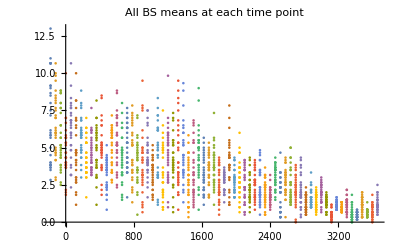

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

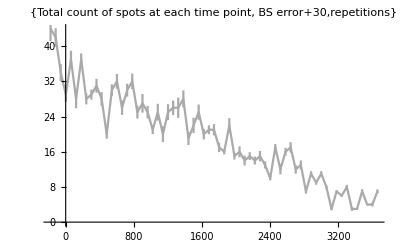

```mathematica
ErrorListPlot[b,PlotStyle->{Darker[White]}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```

### BS for Purple Spots:

```mathematica
purple//Dimensions
```

{6,65,2}

```mathematica
purple = purple[[All,All,2]]
```

{{9,10,11,11,11,6,8,7,8,11,7,7,12,7,8,8,5,10,6,9,7,7,6,7,9,6,9,7,12,7,12,12,8,9,8,11,8,7,9,6,6,8,7,10,6,6,7,7,8,8,10,8,9,7,8,9,9,7,7,10,11,6,8,5,10},{44,37,38,34,36,49,41,42,47,38,33,43,41,41,48,41,48,45,49,46,31,45,43,40,41,46,44,49,46,45,46,42,45,37,38,33,41,55,52,44,44,55,50,44,40,49,43,57,48,38,47,42,47,53,40,51,53,39,40,40,44,52,42,46,47},{37,44,26,33,45,40,43,49,37,45,45,51,42,46,43,37,44,44,50,46,48,48,48,49,51,41,46,43,56,52,50,42,40,41,40,40,42,41,37,44,38,39,40,45,47,40,45,46,42,46,46,44,43,47,49,44,41,41,43,40,52,45,48,40,46},{0,0,0,1,2,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,2,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0},{21,20,18,12,10,7,17,15,14,20,17,18,12,13,18,16,23,15,16,9,14,13,10,15,16,19,18,12,13,11,11,9,13,10,13,10,15,13,15,18,14,19,14,21,15,20,18,11,12,12,14,14,8,20,14,9,12,13,16,16,13,13,13,14,17},{40,41,35,39,38,39,34,36,34,31,32,35,39,38,40,36,35,37,36,38,36,32,31,38,30,39,36,34,39,39,36,34,38,37,38,37,35,32,37,37,32,39,39,34,36,40,36,36,38,37,32,37,36,37,35,34,35,32,30,32,37,37,32,36,32}}

```mathematica
(*
DEV: 
I dont think this is right..need one error of all the means instead of the dev of data from each mean 

stdevsBS = Table[Table[StandardDeviation[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]//Transpose;
errorBS = Table[ErrorBar/@stdevsBS[[i]],{i,1,Length@stdevsBS,1}];
b = Table[Transpose[{meanTimeBS[[i]],errorBS[[i]]}],{i,1,Length@meansBS,1}];
Dimensions/@b
Dimensions/@meansBS
meanTimeBS = Table[Transpose[{Table[times,Length@meansBS][[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];

*)
```

```mathematica
a = Table[Table[Table[RandomChoice[purple[[All,i]]],sampleSize],repetitions ],{i,1,Length@purpleSpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

{8.77547,6.73206,6.96068,5.99986,6.36618,9.31016,6.27,7.11209,7.48464,6.26869,6.51578,9.47541,6.66735,9.91946,7.63524,6.47656,6.75598,7.78168,6.72761,8.33393,8.55916,7.50437,6.23108,7.05108,7.5817,6.59023,7.43505,7.35466,8.53623,7.95277,8.52938,6.21393,6.55298,6.75388,5.78636,6.58592,6.66694,7.56855,6.10589,7.57766,7.81961,7.11823,9.31577,5.55249,7.06082,6.8129,6.98506,5.7904,8.08831,6.53138,8.21009,8.16866,7.04983,9.51238,7.62174,7.39503,7.6232,6.66415,5.1896,6.68079,6.75923,6.82739,7.48422,6.57152,6.0066}

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{17.8333,29.1667,5.,30.8333,35.3333,27.3333,19.8333,16.5,34.5,31.1667,40.8333,33.6667,17.,30.5,38.3333,18.8333,20.5,20.,28.6667,22.3333,33.,31.5,20.1667,33.3333,15.1667,13.8333,18.,13.3333,19.3333,17.1667}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{purpleTime ,errorBS}];
```

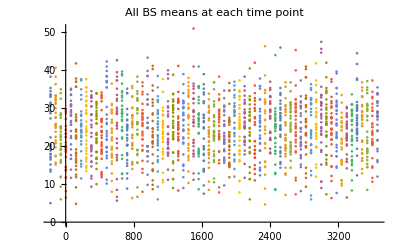

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

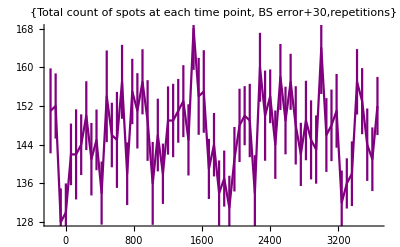

```mathematica
ErrorListPlot[b,PlotStyle->{Purple}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```